#### GHZ States v2 Want to prepare GHZ states as a graph state; Need to devise a series of projections with reasonable binomial factors; This would generalize the procedure for EPR states in https://journals.aps.org/pra/pdf/10.1103/PhysRevA.108.032420

#### Preliminary settings:

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];
```

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];
```

#### Creating the Rotation Matrix and Prefactor:

```mathematica
yRotataionMatrixElem[k_,kp_,θ_,ϕ_]:=Exp[-I*(2*k-Np)*ϕ/2]*Sqrt[((k!)*((Np-k)!)*(kp!)*((Np-kp)!))]*Sum[(((-1.0)^n)*(Cos[θ/2]^(k-kp+Np-2*n))*(Sin[θ/2]^(2*n+kp-k)))/(((k-n)!)*((Np-kp-n)!)*(n!)*((kp-k+n)!)),{n,Max[k-kp,0],Min[k,Np-kp]}];
(*Computes the matrix elements for a rotation around the Y-axis in the bosonic basis*)
(*k, kp are quantum numbers
theta is the rotation angle
phi is the phase*)

psi[k1_,k2_,k3_,k4_]=(1/4^Np)*Sqrt[Binomial[Np,k1]*Binomial[Np,k2]*Binomial[Np,k3]*Binomial[Np,k4]];

(*Computes a prefactor related to the probability amplitudes for the given occupation numbers k1,k2,k3,k4*)
```

```mathematica
yRotataionMatrixElem[k_,kp_,θ_,ϕ_]:=Exp[-I*(2*k-Np)*ϕ/2]*Sqrt[((k!)*((Np-k)!)*(kp!)*((Np-kp)!))]*Sum[(((-1.0)^n)*(Cos[θ/2]^(k-kp+Np-2*n))*(Sin[θ/2]^(2*n+kp-k)))/(((k-n)!)*((Np-kp-n)!)*(n!)*((kp-k+n)!)),{n,Max[k-kp,0],Min[k,Np-kp]}];
(*Computes the matrix elements for a rotation around the Y-axis in the bosonic basis*)
(*k, kp are quantum numbers
theta is the rotation angle
phi is the phase*)

psi[k1_,k2_,k3_,k4_]=(1/4^Np)*Sqrt[Binomial[Np,k1]*Binomial[Np,k2]*Binomial[Np,k3]*Binomial[Np,k4]];

(*Computes a prefactor related to the probability amplitudes for the given occupation numbers k1,k2,k3,k4*)
```

#### Parameters

```mathematica
Np=2; (*Number of bosons*)
dim=(Np+1)^4;(*Total dimension of the Hilbert space*)
θ=Pi/2;
ϕ=0;

(*Create the cluster state*)
clusterstate=ArrayReshape[Table[KroneckerDelta[k1,k2]*KroneckerDelta[k3,k4]*Sum[((-1)^(Np-k1-k3+l))*Binomial[k1,l]*Binomial[Np-k1,k3-l]/Binomial[Np,k3],{l,0,Min[k1,k3]}],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np}],{1,(Np+1)^4}][[1]];
clusterstate=N[Normalize[clusterstate]];
```

#### Projection, Rotation Matrices; Initial Psi

```mathematica
(*Projection matrix*)
```

```mathematica
projmatz=ArrayReshape[Table[KroneckerDelta[k1,k1p]*KroneckerDelta[k2,k2p]*KroneckerDelta[k3,k3p]*KroneckerDelta[k4,k4p]*KroneckerDelta[k1,k2]*KroneckerDelta[k3,k4],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np},{k4p,0,Np}],{(Np+1)^4,(Np+1)^4}];

(*Initial Psi vector*)
psivec0=ArrayReshape[Table[psi[k1,k2,k3,k4],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np}],{1,(Np+1)^4}][[1]];

(*Rotation around Y axis for qubits 1 and 2*)
Urot12=ArrayReshape[Table[yrotmatelem[k1p,k1,θ,ϕ]*yrotmatelem[k2p,k2,θ,ϕ]*KroneckerDelta[k3,k3p]*KroneckerDelta[k4,k4p],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np},{k4p,0,Np}],{(Np+1)^4,(Np+1)^4}];

(*Rotation around Y axis for qubits 3 and 4*)
Urot34=ArrayReshape[Table[yrotmatelem[k3p,k3,θ,ϕ]*yrotmatelem[k4p,k4,θ,ϕ]*KroneckerDelta[k2,k2p]*KroneckerDelta[k1,k1p],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np},{k4p,0,Np}],{(Np+1)^4,(Np+1)^4}];
```

```mathematica
targetlist123={};
targetlist234={};
targetlist123b={};

(*Appending valid states to the respective target list *)
For[k1=0,k1≤Np,k1=k1+1,
For[k2=0,k2≤Np,k2=k2+1,
For[k3=0,k3≤Np,k3=k3+1,
For[k4=0,k4≤Np,k4=k4+1,
If[(k1+k2+k3-Np≥0),
targetlist123=Append[targetlist123,{k1,k2,k3,k4}];
];
If[(-k1+k2-k3+Np>=0),
targetlist123b=Append[targetlist123b,{k1,k2,k3,k4}];
];
If[(k2+k3+k4-Np≥0),
targetlist234=Append[targetlist234,{k1,k2,k3,k4}];
];
];
];
];
];

(*More projection matrices*)
projmatx1230=ArrayReshape[Table[KroneckerDelta[k1,k1p]*KroneckerDelta[k2,k2p]*KroneckerDelta[k3,k3p]*KroneckerDelta[k4,k4p]*If[MemberQ[targetlist123,{k1,k2,k3,k4}],1,0],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np},{k4p,0,Np}],{(Np+1)^4,(Np+1)^4}];

projmatx123b0=ArrayReshape[Table[KroneckerDelta[k1,k1p]*KroneckerDelta[k2,k2p]*KroneckerDelta[k3,k3p]*KroneckerDelta[k4,k4p]*If[MemberQ[targetlist123b,{k1,k2,k3,k4}],1,0],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np},{k4p,0,Np}],{(Np+1)^4,(Np+1)^4}];

projmatx2340=ArrayReshape[Table[KroneckerDelta[k1,k1p]*KroneckerDelta[k2,k2p]*KroneckerDelta[k3,k3p]*KroneckerDelta[k4,k4p]*If[MemberQ[targetlist234,{k1,k2,k3,k4}],1,0],{k1,0,Np},{k2,0,Np},{k3,0,Np},{k4,0,Np},{k1p,0,Np},{k2p,0,Np},{k3p,0,Np},{k4p,0,Np}],{(Np+1)^4,(Np+1)^4}];

(*Conjugating the projection matrices by the Y-axis rotation, effectively switching bases*)
projmatx123=ConjugateTranspose[Urot12].projmatx1230.Urot12;
projmatx123b=ConjugateTranspose[Urot12].projmatx123b0.Urot12;
projmatx234=ConjugateTranspose[Urot34].projmatx2340.Urot34;
```

```mathematica
sol=Eigensystem[projmatz.projmatx234.projmatx123.projmatx123b];
sol[[1]]
```

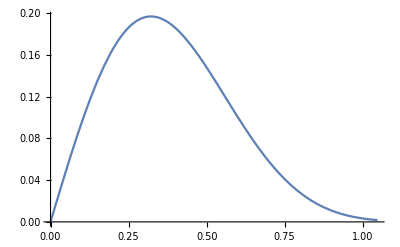

```mathematica
nd=1;nc=10-nd;
Plot[{(Cos[x]^nc)*(Sin[x]^nd)},{x,0,Pi/(Sqrt[nc])},PlotRange->All]
```

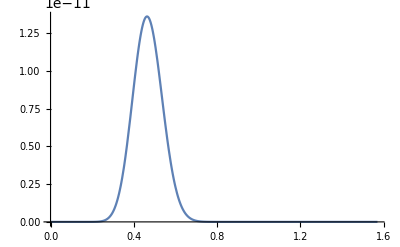

```mathematica
nd=20;nc=100-nd;
Plot[{(Cos[x]^nc)*(Sin[x]^nd)},{x,0,Pi/2},PlotRange->All]
```